```mathematica
e=1;
m=4;
P=2^m;
Ep=10;
ΔCi=Table[0,{i,1,Ep}];
ΔNi=Table[0,{i,1,Ep}];
W$=Table[0,{i,1,Ep}];
WMG=Table[0,{i,1,Ep}];
WBG=Table[0,{i,1,Ep}];
PT=Table[0,{i,1,Ep}];
Dynamic[{e,t}]
```

```mathematica
(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=2000-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[190,{i,1,n}];
c=Table[100,{i,1,n}];
NStock=Table[9,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
BScollect=Table[0,{i,1,n}];
"initial set";
Do[
Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^P-1}],2,P]];
Do[Action⟦1,k⟧=(2*Action⟦1,k⟧-1),{k,1,P}];
RandomStrategy=Action;
AgentStrategy⟦i,s⟧=Flatten[RandomStrategy,1],{s,1,S},{i,1,n}]
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];
Do[If[BS⟦i,1⟧==AgentStrategy⟦i,1⟧,BScollect⟦i⟧=BScollect⟦i⟧+1,BScollect⟦i⟧=BScollect⟦i⟧-1],{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
"signal=UnitStep[MarketAction]";
"match order & Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];Do[NStock⟦i,2⟧=9,{i,1,n}];Do[W⟦i⟧=190,{i,1,n}];,
Do[NStock⟦i,1⟧=NStock⟦i,2⟧,{i,1,n}];
ap={};
an={};
Do[If[Positive[BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧],AppendTo[ap,i],AppendTo[an,i]],{i,1,n}];
If[Length[ap]>Length[an],ap1=RandomSample[ap,Length[an]];Do[c⟦ap1⟦i⟧⟧=c⟦ap1⟦i⟧⟧-BS⟦ap1⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧),{i,1,Length[an]}];
Do[NStock⟦ap1⟦i⟧,2⟧=NStock⟦ap1⟦i⟧,1⟧+BS⟦ap1⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,Length[an]}];Do[c⟦an⟦i⟧⟧=c⟦an⟦i⟧⟧-BS⟦an⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧),{i,1,Length[an]}];
Do[NStock⟦an⟦i⟧,2⟧=NStock⟦an⟦i⟧,1⟧+BS⟦an⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,Length[an]}],
an1=RandomSample[an,Length[ap]];
Do[c⟦ap⟦i⟧⟧=c⟦ap⟦i⟧⟧-BS⟦ap⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧),{i,1,Length[ap]}];
Do[NStock⟦ap⟦i⟧,2⟧=NStock⟦ap⟦i⟧,1⟧+BS⟦ap⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,Length[ap]}];
Do[c⟦an1⟦i⟧⟧=c⟦an1⟦i⟧⟧-BS⟦an1⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧),{i,1,Length[ap]}];
Do[NStock⟦an1⟦i⟧,2⟧=NStock⟦an1⟦i⟧,1⟧+BS⟦an1⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,Length[ap]}];];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);,{i,1,n}];];
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Goto[sample],Goto[begin]];
Label[sample];
ΔCi⟦e⟧=c⟦2⟧;
ΔNi⟦e⟧=NStock⟦2,2⟧;
W$⟦e⟧=W⟦1⟧;
WMG⟦e⟧=W⟦2⟧;
WBG⟦e⟧=Mean[W⟦1;;n⟧];
PT⟦e⟧=Price⟦T⟧;
e=e+1; 
If[e>Ep,Break,Goto[New]];)//AbsoluteTiming
```

{229.81614,Null}

```mathematica
4626/3600//N
```

1.285

```mathematica
Q=1/n Sum[(2/T*BScollect⟦i⟧)^2,{i,1,n}]//N
```

0.438852

```mathematica
N[Table[{ΔCi⟦e⟧-100,9*(PT⟦e⟧-10),(ΔNi⟦e⟧-9)*PT⟦e⟧,PT⟦e⟧,(ΔNi⟦e⟧-9)},{e,1,Ep}]]
```

{{-894.825,28.6571,1292.04,13.1841,98.},{-4875.43,12.5375,4557.22,11.3931,400.},{-990.049,-17.9107,817.012,8.00993,102.},{2795.93,14.3285,-2805.28,11.5921,-242.},{3000.06,32.2392,-3490.61,13.5821,-257.},{-368.506,-37.6124,273.58,5.82084,47.},{-1878.91,25.0749,1738.91,12.7861,136.},{3713.67,-28.6571,-3005.8,6.81588,-441.},{1444.18,5.3732,-1568.36,10.597,-148.},{-650.948,28.6571,553.733,13.1841,42.}}

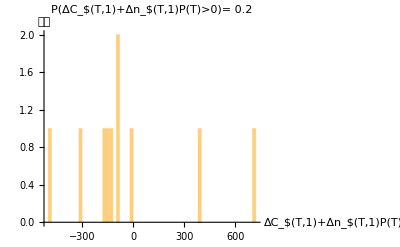

```mathematica
Histogram[Flatten[Table[{ΔCi⟦e⟧-100+(ΔNi⟦e⟧-9)*PT⟦e⟧},{e,1,Ep}],1],{20},AxesLabel->{"ΔC_$(T,1)+Δn_$(T,1)P(T)",次數},PlotLabel->"P(ΔC_$(T,1)+Δn_$(T,1)P(T)>0)= "<>ToString[N[(Total[UnitStep[Table[{ΔCi⟦e⟧-100+(ΔNi⟦e⟧-9)*PT⟦e⟧},{e,1,Ep}]]]⟦1⟧)/Ep]]]
```

```mathematica
N[(Total[UnitStep[Table[{ΔCi⟦e⟧-100+(ΔNi⟦e⟧-9)*PT⟦e⟧},{e,1,Ep}]]]⟦1⟧)/Ep]
```

0.765

```mathematica
N[WMG-190]
```

{425.876,-305.675,-190.948,4.97519,-458.314,-132.539,-114.927,679.212,-118.807,-68.5581}

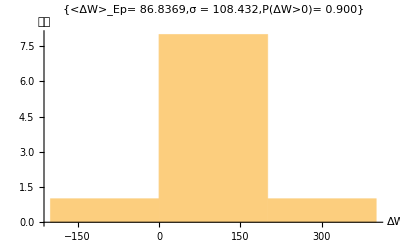

```mathematica
Histogram[W$-190,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[W$-190]]],"σ = "<>ToString[N[StandardDeviation[W$-190]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[W$-190]],3]]}]
```

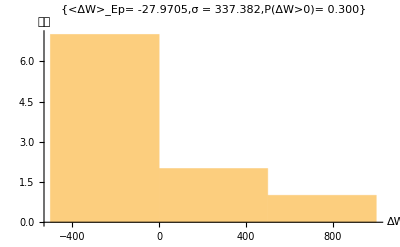

```mathematica
Histogram[WMG-190,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[WMG-190]]],"σ = "<>ToString[N[StandardDeviation[WMG-190]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[WMG-190]],3]]}]
```

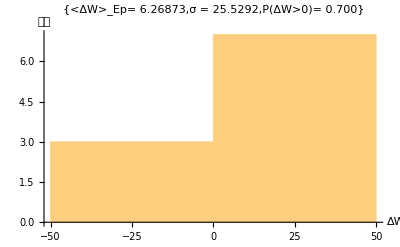

```mathematica
Histogram[WBG-190,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[WBG-190]]],"σ = "<>ToString[N[StandardDeviation[WBG-190]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[WBG-190]],3]]}]
```

```mathematica
t1=0;
t2=T;
f1=ListPlot[A,AxesLabel->{"t","A"},PlotRange->{{t1,t2},{-n,n}},Joined->True,PlotLabel->"<A>_(T - 1)= "<>ToString[N[Mean[A⟦t1+1;;t2-1⟧]]]]
f2=ListPlot[Price⟦t1+1;;t2⟧,AxesLabel->{"t","Price"},PlotRange->Automatic,Joined->True,PlotLabel->"P(T)= "<>ToString[N[Price⟦T⟧,4]]]
f3=Histogram[A⟦t1+1;;t2⟧,AxesLabel->{"A","Number"}]
```

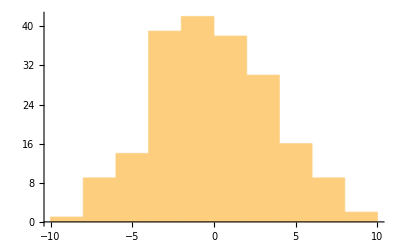

```mathematica
Histogram[PT-10]
```